## XPL: Logistic Regression

## Data Set: HR Employee Attrition and Performance

## File Header

Version: 5.3UA
Filename: XPL_LogisticExpr_sr_v.5.3UA.nb
Version Author: Shishir Reddy
Originating Author: Shishir Reddy, Jenny Li, Kevin Lin
Date: 10/4/16

## Designer’s Intent

### Use a Logistic Regression to model an employee’s attrition as a function of other variables such as:

Age 
Business Travel
Daily Rate
Department
Distance From Home
Education
Education Field
Employee Count
Employee Number
Environment Satisfaction
Gender
Hourly Rate
Job Involvement
Job Level
Job Role
Job Satisfaction
Marital Status
Monthly Income
Monthly Rate
Number of Companies Worked
Over Time
Percent Salary Hike
Performance Rating
Relationship Satisfaction
Standard Hours
Stock Option Level
Total Working Years
Training Times Last Year
Work Life Balance
Years At Company
Years In Current Role
Years Since Last Promotion
Years With Current Manager

### Organization:

#### 1. Convert Imported Data Into Quantitative Data (Hyperlink) 1.1. Importing Data and Remove Skewed Columns 1.1.1. Information for Employee Attrition and Performance 1.1.2. Remove skewed columns 1.2. Select the Dependent (functional) Variable 1.2.1. Extract data from any column with pure function 1.2.2. Attrition is the selected dependent variable 1.3. Separate the Quatitative and Qualitative Data 1.3.1. Quantitative: remove words and leave numerical data 1.3.2. Qualitative: remove integers and leave non-numerical data 1.4. Use Reference Category Coding to Convert Qualitative Data 1.4.1. Convert qualitative data into numbers 1.4.1.1. Make n - 1 columns that represent every factor except for one 1.4.1.2. Assign quantitative values 1.4.1.3.1. If element is factor, give it a (1) 1.4.1.4.2. If element is not a factor, give it a (0) 1.5. Clean up and Show the New Data 1.5.1. Combine data, which is all quantitative 1.6. Convert Attrition Column into Numbers 1.6.1. Change Yes and True --1 1.6.2. Change No and False --2

#### 2. Create a Logistic Model (Hyperlink) 2.1. Define the Independent and Function Variables 2.1.1. Create new variables for independent and functional variable data 2.2. Combine the Independent and Functional Variables into a Set of Ordered Pairs 2.2.1. Combine data into single data set 2.2.1.1. Use Transpose 2.3. Insert Data into Logistic Function 2.3.1. Use LogitModelFit to model data with logistic function 2.4. Plot the Data Points 2.4.1. Graph the function 2.5. Add other Input Variables 2.5.1. Allow unlimited number of inputs into logistic model 2.3.2.1. Non-numerical inputs are changed into numbers 2.5.2. Test model 2.3.3.1. Use sample employee profiles

#### 3. Analyze the Data (Hyperlink) 3.1. Determine the Statistical Significance 3.1.1. Determine level of impact on attrition and positive or negative impact 3.1.1.1. Estimate 3.1.1.2. Standard Error 3.1.1.3. z-Statistic 3.1.1.4. p-value 3.2. Visualize the Data with Bubble Chart 2.2.1. Visualize impact on attrition 2.2.1.1. Bigger bubble means more people are in that group 2.2.1.2. Bubbles higher up mean more likely to leave company

#### 4. User Interface (Hyperlink) 4.1. Develop Easier Means of Importing Data 4.1.1. Create function to import data from URL 4.1.2. Allow user to import data from file 4.1.3. Apply functions to respective buttons 4.1. Create Customer Profile

## 1. Convert imported data into quantitative data

### 1.1 Import Data and Remove Skewed Columns

#### Designer’s Intent

Store independent and dependent variables for use in the logistic function
Remove columns containing the repeated numbers

#### Pseudocode

Use Import to import the data
Each column is a list for a different input variable
	e.g. BusinessTravel, Gender, DistanceFromCompany	

Define new variable listSkewedColumns
	Use Table to list all columns that consist of one value that remains the same
	Run test SameQ 
		If all the data within a column is the same, it returns True 

Define new variable cleanData
	Delete the skewed columns from the data

Show cleanData

#### Code

```mathematica
data=Import["https://community.watsonanalytics.com/wp-content/uploads/2015/03/WA_Fn-UseC_-HR-Employee-Attrition.xlsx"][[1]];
(*data=%[[1]]*)(*import the first sheet of the data containing all the values*)
(*data[[1;;5]]//TableForm (*Rows 1-5*)*) 
listSkewedColumns = (Table[And@@(SameQ[data[[2,n]],data[[#,n]]]&/@Range[2,Length[data]]),{n,1,Length@data[[1]]}]);
cleanData = Delete[data[[#]],
(Position[ listSkewedColumns,True])(*Position gives positions of functions that are skewed*)
]&/@Range[Length[data]];
(*Range for all rows of data *)
```

### 1.2 Clean Special Characters in headers

#### Designer’s Intent

Create a new function that can output data from any column, given the variable name

#### Pseudocode

Define new function findData 
	Input: name of any column
	Output: data from the column 
		(*See Alex for more information*)

#### Code

```mathematica
findData[name_,data_]:=(data[[#]]&/@Range[2,Length[data]])[[All,Flatten[Position[data[[1]],name[[#]]]&/@Range[1,Length[name]]]]]
(* Input: name of the column. Output: the corresponding column *)

deleteDuplicatesData = DeleteDuplicates[cleanData[[2;;Length[cleanData],#]] (*deletes all duplicates inside the qual data*)
]&/@Range[Length[cleanData[[1]]]];(*Range is the number of different qualitative variables *) 

cleanDataNoSpecialChars = Prepend[ (*Prepend adds the new cleaned first row back to the top*)
Drop[cleanData,{1}],StringReplace[cleanData[[1]],{"|<"->"","\\/"->"","]"->"","><"->"","_"->"","."->"",","->"","'"->""," "-> "", "&"-> "","("->"",")"->"","{"->"","}"->"","-"->""}] ];

binaryColumns = (cleanDataNoSpecialChars[[1,#]]&/@Flatten@Position[Length/@deleteDuplicatesData,2]);
(*Used to select functional variable in next section*)

binaryColumns = Delete[binaryColumns,Position[(findData[binaryColumns,cleanDataNoSpecialChars])[[1]],x_/;NumericQ[x]&&x>1 ]];
```

### 1.3 Select the Functional Variable

#### Designer’s Intent

Select a dependent variable
Assign a new variable name to the dependent variable’s column

#### Pseudocode

Select independent variable (independentVar)
Define the dependent variable’s name as a new variable functionalName

Join functionalName and its data (findData) in a new variable functionalVarColumn

Drop the functional variable from cleanData(it will be handled separately).

#### Code

```mathematica
functionalName = binaryColumns[[1]];
```

### 1.4 Dropping the Functional Variable

#### Designer’s Intent

Select a dependent variable
Assign a new variable name to the dependent variable’s column

#### Pseudocode

Select independent variable (independentVar)
Define the dependent variable’s name as a new variable functionalName

Join functionalName and its data (findData) in a new variable functionalVarColumn

Drop the functional variable from cleanData(it will be handled separately).

#### Code

```mathematica
functionalVarColumn = Join[{functionalName},Flatten@findData[{functionalName},cleanDataNoSpecialChars]];(*joins functional variable and its data*)

cleanDataNoFunctionalColumn =Drop[cleanDataNoSpecialChars//Transpose,Flatten@Position[cleanDataNoSpecialChars[[1]],functionalName] (*drop functional variable, since it's the function*)
]//Transpose;
```

### 1.5 Enter Employee Profile (UNDER DEVELOPMENT)

#### Designer’s Intent

Enter the employee profile with data corresponding with the original dataset

#### Pseudocode

UI

#### Code

```mathematica
badEmployeeProfile={35,"Travel_Frequently",700,"Research & Development",1.5,4,"Other",2069,1,"Male",60,2,1,"Healthcare Representative",1,"Divorced",5000,10000,2,"Yes",14,2,1,1,3,1,1,3,3,3,3};

goodEmployeeProfile={35,"Travel_Frequently",1324,"Sales",10,8,"Marketing",2070,4,"Male",90,4,3,"Sales Executive",4,"Married",18000,23000,2,"Yes",15,4,4,1,4,4,7,4,4,9,9};
```

### 1.6 Separate the Quantitative and Qualitative data

#### Designer’s Intent

Turn the numerical and qualitative data into two separate lists
	in order to convert qualitative data (words) to numbers next

#### Pseudocode

Create new variable numData
	Delete all qualitative data (words) and leave the numerical data

Create new variable qualData
	Delete all integers and real numbers, leaving just qualitative (non-numerical) data

#### Code

```mathematica
cleanDataWithProfile = Append[cleanDataNoFunctionalColumn,badEmployeeProfile];

numData = Delete[cleanDataWithProfile[[#]],(*Deletes all strings*)
Position[cleanDataWithProfile[[2]],_String] (*_String is part of Position function, gives list of qualitative data starting from row 2*)
]&/@ Range[Length[cleanDataWithProfile]];(*goes through all rows of data*)

badEmployeeProfileNum = Piecewise[{{{},numData=={}},{numData[[Length@numData]],numData≠{}}}];

numData = Piecewise[{{numData,numData=={}},{Drop[numData,{Length@numData}],numData≠{}}}];

qualData = (* separates qualitative data into its own list *)
Delete[cleanDataWithProfile[[#]],
Join[Position[cleanDataWithProfile[[2]],_Real],Position[cleanDataWithProfile[[2]],_Integer]](*Takes out all data that is either a real number or an integer*)
]&/@Range[Length[cleanDataWithProfile]];
```

### 1.7 Use Reference Category Coding to Convert Qualitative Data

#### Designer’s Intent

Convert the qualitative data into numbers
Reference category coding:
	Each column of qualitative data is comprised of n different elements 
		Ex: BusinessTravel column has 3 factors (n=3): Travel_Frequently, Travel_Rarely, Non-Travel
	(1) Create new columns for n-1 factors
		2 new columns ((3)-1) are created for 2 of the 3 factors
		Ex: Travel_Frequently and Travel_Rarely
	(2) Attach the name of the original column to each factor’s name
		Travel_Rarely-> BusinessTravel▼Travel_Rarely
		New factor columns have the same data as the original column (BusinessTravel)
	(3) Under each factor column, replace the factor name with a 1, otherwise leave the other factors as 0
		In the set of data under the Travel_Rarely column, Travel_Rarely-> 1, and Travel_Frequently-> 0, Non-Travel-> 0
		Likewise under Travel_Frequently, Travel_Frequently-> 1, and the other factors become 0
	(4) For the leftover factor without a column, it will be listed as 0 in the other factor columns 
		Since there is no Non-Travel column, Non-Travel is indicated when both Travel_Rarely-> 0 and Travel_Frequently-> 0
	(5) Delete the original column, leaving only the factor columns

#### Pseudocode

Define new variable deleteDuplicatesQual
	 Delete duplicate data in each column and return each set of factors as a list
	 	Use DeleteDuplicates to
		Ex: For BusinessTravel column, returns {Travel_Rarely,Travel_Frequently, Non-Travel}, followed by the next column’s set of factors
Store just the data (without variable names) from qualData as a new variable qualColumns

Define new variable qualToNumColumns to perform reference category coding 
	Using Table and Join
		Use StringJoin to set the names of each new column
		Apply rules to qualColumns to turn each factor name under its respective column into 1
		Make Table to turn the other remaining factors into 0
		Use Cases[Except[factor column]] to specify these remaining factors
			Ex: Picks out {Travel_Frequently, Non-Travel} from under the Travel-Rarely column and converts them each to 0

#### Code

```mathematica
deleteDuplicatesQual = DeleteDuplicates[qualData[[2;;Length[cleanDataWithProfile],#]] (*deletes all duplicates inside the qual data*)
]&/@Range[Length[qualData[[1]]]];(*Range is the number of different qualitative variables (e.g. BusinessTravel, Gender, MaritalStatus)*) 

qualColumns = findData[qualData[[1]],cleanDataWithProfile]; (*Reminder: findData is a function from section 1.2*)

qualToNumColumns = Flatten[ (*removes extra curly brackets*)
Table[
Join[
{StringJoin[qualData[[1,i]],"▼",deleteDuplicatesQual[[i,#]]]},(*joins original column name, ▼, and each factor column name*)

(*transforming the data into 1s and 0s*)
(*first, transform the factor that matches each factor column's name into 1*)
qualColumns[[All,i]] (*goes through all of each set of factors (i) *)
/.Join[{deleteDuplicatesQual[[i,#]]->1},(*assigns 1 to each factor under its corresponding column*) (*item (3) in Designer's Intent*)

(*next, transform everything else to 0*)
Table[
Cases[ deleteDuplicatesQual[[i]],(*goes through each set in the deleteDuplicates list*)
Except[ deleteDuplicatesQual[[i,#]]]] (*picks out all the remaining data under each factor column*)
[[n]]-> 0,{n,1,Length@Cases[deleteDuplicatesQual[[i]],Except[deleteDuplicatesQual[[i,#]]]]}]]  
(*itinerates through each part of the list of remaining factors, e.g. {Travel-Freq, Non-Travel}, and turns each of them into 0s*)

]&/@Range[Length@deleteDuplicatesQual[[i]]-1],(*# goes through each of the n-1 columns, e.g. leaving out Non-Travel *)
{i,1,Length@deleteDuplicatesQual}] (*i goes through each set of factors, e.g. BusinessTravel, Department, etc. *)
,1 (*flattens at one level*)
];

qualToNumColumns =Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{Transpose[qualToNumColumns],qualToNumColumns≠{}}}];(*If there were no qualitative columns to begin with, Transpose would return an error due to evaluation on an empty list.*)

badEmployeeProfileQual = Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{qualToNumColumns[[Length@qualToNumColumns]],qualToNumColumns≠{}}}];

qualToNumColumns =Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{ Drop[qualToNumColumns,{Length@qualToNumColumns}],qualToNumColumns≠{}}}];

badEmployeeProfile = Join[badEmployeeProfileNum,badEmployeeProfileQual];
```

### 1.8 Clean up and Show the New Data

#### Designer’s Intent

Combine the now-quantitative data from 1.4 back with the numerical data
Show the new data as a table

#### Pseudocode

Update cleanData to Join back numerical data (numData) with the qualitative data that is now numerical (qualToNum)
	Also Join back the fuctional variable column

Update cleanData again to Prepend a cleaner version of the first row of variable names
	Remove unncessary syntax in the variable names using rules
		e.g. “_” --> “ “ (blank)

#### Code

```mathematica
cleanDataAllQuantitative = Join[ (*Join functional variable column in at the end*)
(Join[numData,qualToNumColumns,2 (*Join the new columns with numData at level 2*)
])//Transpose (*Transpose joins the data together as a new column*)
,{functionalVarColumn}]//Transpose; (*Tranpose sorts data into row by column*)

cleanDataFinalNoChars = Prepend[ (*Prepend adds the new cleaned first row back to the top*)
Drop[cleanDataAllQuantitative,{1}],StringReplace[cleanDataAllQuantitative[[1]],{"|<"->"","\\/"->"","]"->"","><"->"","_"->"","."->"",","->"","'"->""," "-> "", "&"-> "","("->"",")"->"","{"->"","}"->"","-"->""}] ];
```

### 1.9 Convert Binary Functional Variable Column into Numerical Data

#### Designer’s Intent

Change the functional variable data, if binary, into numbers for easier use
	Column is still in terms of Yes/No or True/False

#### Pseudocode

Use rules to change binary data into numbers
	Yes → 1
	No → 0
	True → 1
	False → 0

#### Code

```mathematica
cleanDataFinal =cleanDataFinalNoChars/.{"Yes"->1,"No"->0,"True"-> 1,"False"->0,"Male"->1,"Female"->0};
(*binary qualitative data is handled separately because YES and TRUE must be set to 1 in order to calculate the percent likelihood that the employee will leave. Otherwise the percent likelihood that the employee will stay would be returned*)
```

```mathematica
cleanDataFinal;
```

## 2. Create a Logistic Model

### 2.1 Define the Independent Variable

#### Designer’s Intent

Select an independent variable

#### Pseudocode

Select independent variable (independentVar)

#### Code

```mathematica
independentVarName = (Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]])[[1]];
```

### 2.2 Combine the Independent and Functional Variables into a Set of Ordered Pairs

#### Designer’s Intent

Combine functional variable data and YearsInCurrentRole data into a single data set

#### Pseudocode

Combine data sets independentVar and functionalVar
	Use Transpose 
		Make sure functional variable is last
	New data is in the form {years in current role, functional variable}

#### Code

```mathematica
independentVar = Flatten@findData[{independentVarName},cleanDataFinal];(*independent variable data (for logistic plot)*)

newData=findData[{"YearsAtCompany","JobInvolvement","Attrition"},cleanDataFinal];(*combines datasets with independent variable as "x" and dependent variable as "y"*)
```

### 2.3 Insert Data into Logistic Function

#### Designer’s Intent

Use the functional variable data stored above and turn it into a function

#### Pseudocode

Create logistic function using the new set of data
	Use LogitModelFit

#### Code

```mathematica
logitContour=LogitModelFit[newData,{varOne,varTwo},{varOne,varTwo}] (*create logistic function with attrition data*)
```

FittedModel[1/(1+ⅇ^(-0.140699+0.0805919 varOne+0.489218 varTwo))]

### 2.4 Plot the Data Points as a Logistic Function

#### Designer’s Intent

Visualize data from the function in a line plot

#### Pseudocode

Function to plot logit
	Use Plot 
	Bounds are from 0 to the maximum value of the independent variable
AxesLabel shows the variables the function is plotting

#### Code

```mathematica
newData=findData[{"YearsAtCompany","JobInvolvement","Attrition"},cleanDataFinal];
```

```mathematica
newData=findData[{"YearsAtCompany","JobInvolvement","Attrition"},cleanDataFinal];
logitContour=LogitModelFit[newData,{varOne,varTwo},{varOne,varTwo}]
```

FittedModel[1/(1+ⅇ^(-0.140699+0.0805919 varOne+0.489218 varTwo))]

```mathematica
orderedPairs = Drop[newData[[#]],{3}]&/@Range@Length@newData;
cfe=Function[{y},Piecewise[{{Red,y==1},{Darker[Green],y==0}}]];
newerData=Style[orderedPairs[[#]],cfe@(newData[[#,3]])]&/@Range@Length@newData;
```

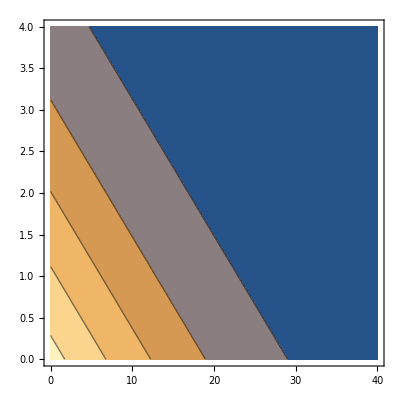

```mathematica
newData=findData[{"YearsAtCompany","JobInvolvement","Attrition"},cleanDataFinal];
logitContour=LogitModelFit[newData,{x,y},{x,y}];
orderedPairs = Drop[newData[[#]],{3}]&/@Range@Length@newData;
cfe=Function[{y},Piecewise[{{Red,y==1},{Darker[Green],y==0}}]];
newerData=Style[orderedPairs[[#]],cfe@(newData[[#,3]])]&/@Range@Length@newData;
ContourPlot[logitContour[x,y],{x,0,40},{y,0,4}]
```

```mathematica
ListPointPlot3D[Table[logitContour[x,y],{x,0,40},{y,0,4}]]
```

-Graphics3D-

### 2.5 Add Other Input Variables

#### Designer’s Intent

Adjust the program to include an unlimited number of inputs (instead of just one or two)
	For data without numerical inputs, 
		Change the data into numbers

#### Pseudocode

Create new variable newData to put all the variables together

Insert all variables into logistic model 
	Use LogitModelFit

Test the model using sample employee profiles

#### Code

```mathematica
newData = Drop[cleanDataFinal,{1}];
(* Drops the first row with all the column names *)
logitFull =LogitModelFit[newData,Symbol/@Flatten@Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]], Symbol/@Flatten@Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]]] (*add all non-skewed variables into logit function*)
```

FittedModel[1/(1+ⅇ^(-4.01807+«61»+0.136702 YearsWithCurrManager))]

```mathematica
logitFull@@badEmployeeProfile
```

0.826757

```mathematica
(*testing the model*)
```

```mathematica
(*logit[35,700,5,10,2069,1,60,2,1,2,2000,10000,1,7,2,1,1,2,2,1,2,2,2,2,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1] 
(*Bad employee profile: *)*)
```

```mathematica
(*logit[35,1324,5,8,2070,4,90,4,3,4,18000,23000,1,18,4,4,1,7,4,4,9,3,3,3,0,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1] 
(*Good employee profile: *)*)
```

## 3. Analyze the Data

### 3.1 Determine the Statistical Significance

#### Designer’s Intent

Find 
	Variables that are statistically significant
	The level of impact on functional variable
	Whether they positively or negatively impact functional variable
Determine statistics  
	Estimate
	Standard Error
	z-Statistic 
	p-value

#### Pseudocode

Use the ParameterTable entry in the LogitFunction

#### Code

```mathematica
logitFull["ParameterTable"]; (*legend: 
P-Value -> Determines statistical significance. As long as the value is less than 0.05, the variable is considered statistically significant, but the closer to 0 the better
z-Statistic -> Shows magnitude of the correlation between variable and function (attrition). Variable with the greatest absolute value of the z-Statistic has the greatest impact on attrition
Standard Error -> Standard Error of regression coefficient
Estimate -> Also known as regression coefficient. Sign of Estimate determines whether the variable has a positive or negative impact on attrition. In this case,  a positive value increases the chance of attrition, or the likelihood that the employee will leave the company*)

tableEntries = Drop[logitFull["ParameterTableEntries"],{1}];
(*each row from the table is turned into a list. First row, the intercept, is dropped because it is not used for correlation*)

reliableData = Join[(*Joins the following two lists together to form a new set of lists*) (*Variable names (Age, DailyRate, etc.) become the first column now*)
(*first list*)
cleanDataFinal[[1,#]](*gives all the variable names (row 1) that have p-values less than 0.05*)
&/@ Position[tableEntries[[All,4]],x_/;x<0.05],(*goes through the fourth column (p-value) in all the rows of the ParameterTable, and returns the position of rows with p-value>0.05*)
(*second list*)

Delete[tableEntries,Position[tableEntries[[All,4]],x_/;x>0.05]](*finds position of rows with p-value>0.05, and deletes these rows from tableEntries*)
,2];(*joins data at the second level*)

sortedReliableData = SortBy[(*default sorts by least to greatest*)
reliableData,
-Abs@#[[4]]&];(*sorts by absolute numerical data in the 4th column (z-value) using Abs*)(*abs value of z value will give the magnitude of correlation*)

groups = GatherBy[sortedReliableData,Positive@#[[2]]&];

cf=Function[{y},Piecewise[{{Red,y>0},{Darker[Green],y<0}}]];

orderedColorSignificance=Style[#[[1]],cf@(#[[2]])]&/@sortedReliableData;

styleTable = Grid[
(*add column labels*)Prepend[
(*pair up attribute & significance*){#,Position[orderedColorSignificance,#][[1,1]]}&/@
orderedColorSignificance[[1;;5]],
{"Variable","Significance"}],
(*making the table look more organized*)Dividers->{2->Black,2->Black},Spacings->{1,.5},Alignment->{{Right,Left},Center}
]

styleTableNegative = Grid[
(*add column labels*)Prepend[
(*pair up attribute & significance*){Style[top5PositiveImpact[[#,1]],Red],#}&/@
Range@Length@top5PositiveImpact,
{"Variable","Positive Significance"}],
(*making the table look more organized*)Dividers->{2->Black,2->Black},Spacings->{1,.5},Alignment->{{Right,Left},Center}
];

styleTablePositive = Grid[
(*add column labels*)Prepend[
(*pair up attribute & significance*){Style[top5NegativeImpact[[#,1]],Darker[Green]],#}&/@
Range@Length@top5NegativeImpact,
{"Variable","Positive Significance"}],
(*making the table look more organized*)Dividers->{2->Black,2->Black},Spacings->{1,.5},Alignment->{{Right,Left},Center}
];

contourVariableOne = (reliableData//Transpose)[[1,1]];
contourVariableTwo = (reliableData//Transpose)[[1,2]];
```

Variable | Significance
OverTime▼Yes | 1
EnvironmentSatisfaction | 2
JobSatisfaction | 3
NumCompaniesWorked | 4
BusinessTravel▼TravelFrequently | 5

```mathematica
positiveEstimate=Piecewise[{{groups[[1]],groups[[1,1,2]]>0},{{},And@@{Length@groups==1,groups[[1,1,2]]<0}},{groups[[2]],groups[[2,1,2]]>0}}];

negativeEstimate=Piecewise[{{groups[[1]],groups[[1,1,2]]<0},{groups[[2]],(Length@groups>1)&&groups[[2,1,2]]<0},{{},Length@groups==1&&groups[[1,1,2]]>0}}];

Style[Grid[Pick[sortedReliableData,Positive@sortedReliableData[[All,2]]],Alignment->Right],Red]
Style[Grid[Pick[sortedReliableData,Negative@sortedReliableData[[All,2]]],Alignment->Right],Darker[Green]]

top5PositiveImpact = Piecewise[{{positiveEstimate[[1;;5]],Length@positiveEstimate≥5},{positiveEstimate,Length@positiveEstimate≤5}}];

top5NegativeImpact = Piecewise[{{negativeEstimate[[1;;5]],Length@negativeEstimate≥5},{negativeEstimate,Length@negativeEstimate≤5}}];
```

OverTime▼Yes | 1.97893 | 0.193851 | 10.2085 | 1.81632×10^-24
NumCompaniesWorked | 0.194495 | 0.0388375 | 5.00793 | 5.50183×10^-7
BusinessTravel▼TravelFrequently | 1.90918 | 0.411898 | 4.63508 | 3.56799×10^-6
DistanceFromHome | 0.0458507 | 0.0107882 | 4.25007 | 0.0000213708
YearsSinceLastPromotion | 0.173515 | 0.0424245 | 4.08996 | 0.0000431439
MaritalStatus▼Single | 1.17373 | 0.346298 | 3.38935 | 0.000700576
BusinessTravel▼TravelRarely | 1.0269 | 0.379822 | 2.70364 | 0.00685855
YearsAtCompany | 0.0961018 | 0.0389066 | 2.47006 | 0.0135089

EnvironmentSatisfaction | -0.434099 | 0.0830126 | -5.22931 | 1.7014×10^-7
JobSatisfaction | -0.414296 | 0.0815239 | -5.0819 | 3.73674×10^-7
JobInvolvement | -0.526934 | 0.122722 | -4.29373 | 0.0000175694
YearsInCurrentRole | -0.15129 | 0.0455274 | -3.32305 | 0.000890376
RelationshipSatisfaction | -0.265435 | 0.0829168 | -3.20122 | 0.00136848
WorkLifeBalance | -0.372489 | 0.124187 | -2.99943 | 0.00270487
YearsWithCurrManager | -0.136702 | 0.0470327 | -2.90653 | 0.00365459
TrainingTimesLastYear | -0.188422 | 0.0731521 | -2.57576 | 0.010002
Age | -0.0315205 | 0.0135888 | -2.31958 | 0.0203634
Gender▼Female | -0.399168 | 0.184694 | -2.16124 | 0.0306765
TotalWorkingYears | -0.059918 | 0.0293383 | -2.04232 | 0.0411203

### 3.2 Select Variable to be Graphed

#### Designer’s Intent

Select the variable to be graphed in the bubble chart alongside the functional variable
	Choose from the statistically significant variables

#### Pseudocode

Create a ActionMenu with a list of choices contatining only statistically significant variables

#### Code

```mathematica
independentName = orderedColorSignificance[[1]];
```

### 3.3 Visualize the Data with BubbleChart

#### Designer’s Intent

Better visualize an variable’s impact on attrition using a graph
	Use BubbleChart 
		Plots average value of the functional variable over any independent variable
	Chart also shows which time group hold more weight
		(i.e. a bigger circle means more people are in that group, so that group holds more weight)

#### Pseudocode

Define new variable pairs - a list of ordered pairs
	Transpose combines functional variable (y-value) and any input variable into an ordered pair

Define new variable meanvalues
	Take the mean value of attrition for each time group 
		Use Mean 
	Group the pairs by each time group (e.g. one year, two years, etc.) 
		Use GroupBy 
		Returns list of ordered pairs {independent variable, funcitonal variable}

Define new variable sizes 
	Assigns each time group a number corresponding to the amount of people in that group
		Visualizes which groups hold more weight based on the magnitude of sizes

Separate the list from meanvalues into just its x and y components
	Define new variable meanvaluesx -- time in company
	Define new variable meanvaluesy -- mean value of attrition

Combine meanvaluesx, meanvaluesy, and sizes
	Use Transpose  
 Graph the data visualization
 	Use BubbleChart

#### Code

```mathematica
pairs = findData[{ToString@independentName,functionalName},cleanDataFinal]; (* YearsAtCompany vs. Attrition *)
domain = Length[DeleteDuplicates[findData[{ToString@independentName},cleanDataFinal]]];(* Number of distinct values in the YearsAtCompany column *)
meanvalues = Mean[ (* Takes the mean of the list of groups created by GroupBy *)
GroupBy[pairs,First][[#]] (* GroupBy is a rule that sorts all the pairs according to the first element (time), e.g. all the 1-years, 2-years, etc. *)
]&/@Range[ (* Maps each value over the domain of all the time groups*) 
domain];
sizes = (Length[GroupBy[pairs,First][[#]]] )(* GroupBy is a rule that sorts all the pairs according to the first element (time), e.g. all the 1-years, 2-years, etc. *)&/@Range[domain];
(* &/@ maps through each group in the list, giving the length of each group *)
meanvaluesx = meanvalues[[All,1]];
meanvaluesy = meanvalues[[All,2]];
newdata = Transpose[{meanvaluesx,meanvaluesy,sizes}]; (*Combines into a list of ordered triples*)
(*BubbleChart requires 3-dimensional list (ordered triples) for an input*)
bubbleChart = BubbleChart[newdata,BubbleSizes->{.01,0.06}, (* BubbleSizes sets the appropriate size for the bubbles *)
ChartStyle->{"Rainbow"},PlotTheme->"Business",FrameLabel->{independentName,StringJoin["Average ",functionalName]},PlotLabel->StringJoin["Average ",functionalName," vs. ",ToString@independentName],ImageSize->Large,Frame->True,FrameTicks->Automatic,BaseStyle->{FontSize->14}]
```

-Graphics-

## 4. Beta Applications

### 4.1 Test Employee Profile (Implementing UI still, but test works)

```mathematica
(*Bad Employee Profile: {35,"Travel_Frequently",700,"Research & Development",1.5,4,"Other",2069,1,"Male",60,2,1,"Healthcare Representative",1,"Divorced",5000,10000,2,"Yes",14,2,1,1,3,1,1,3,3,3,3}, bad work life balance, divorced, low job satisfaction, low income, little work experience*)
```

```mathematica
(*What is the percent likelihood that this employee will leave the company?*)
logitFull@@badEmployeeProfile
```

0.826757

## 5. Master Manipulate

```mathematica
Manipulate[Switch[tabNumber,
"Logistic Model",
(functionalVarColumn = Join[{functionalName},Flatten@findData[{functionalName},cleanDataNoSpecialChars]];
cleanDataNoFunctionalColumn =Drop[cleanDataNoSpecialChars//Transpose,Flatten@Position[cleanDataNoSpecialChars[[1]],functionalName]
]//Transpose;badEmployeeProfile={35,"Travel_Frequently",700,"Research & Development",1.5,4,"Other",2069,1,"Male",60,2,1,"Healthcare Representative",1,"Divorced",5000,10000,2,"Yes",14,2,1,1,3,1,1,3,3,3,3};cleanDataWithProfile = Append[cleanDataNoFunctionalColumn,badEmployeeProfile];
numData = Delete[cleanDataWithProfile[[#]],
Position[cleanDataWithProfile[[2]],_String]
]&/@ Range[Length[cleanDataWithProfile]];
badEmployeeProfileNum = Piecewise[{{{},numData=={}},{numData[[Length@numData]],numData≠{}}}];
numData = Piecewise[{{numData,numData=={}},{Drop[numData,{Length@numData}],numData≠{}}}];
qualData =
Delete[cleanDataWithProfile[[#]],
Join[Position[cleanDataWithProfile[[2]],_Real],Position[cleanDataWithProfile[[2]],_Integer]]]&/@Range[Length[cleanDataWithProfile]];deleteDuplicatesQual = DeleteDuplicates[qualData[[2;;Length[cleanDataWithProfile],#]]]&/@Range[Length[qualData[[1]]]];
qualColumns = findData[qualData[[1]],cleanDataWithProfile]; 
qualToNumColumns =Flatten[Table[Join[{StringJoin[qualData[[1,i]],"▼",deleteDuplicatesQual[[i,#]]]},
qualColumns[[All,i]] /.Join[{deleteDuplicatesQual[[i,#]]->1},Table[Cases[ deleteDuplicatesQual[[i]],Except[ deleteDuplicatesQual[[i,#]]]]
[[n]]-> 0,{n,1,Length@Cases[deleteDuplicatesQual[[i]],Except[deleteDuplicatesQual[[i,#]]]]}]]]&/@Range[Length@deleteDuplicatesQual[[i]]-1],
{i,1,Length@deleteDuplicatesQual}],1];
qualToNumColumns =Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{Transpose[qualToNumColumns],qualToNumColumns≠{}}}];
badEmployeeProfileQual = Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{qualToNumColumns[[Length@qualToNumColumns]],qualToNumColumns≠{}}}];
qualToNumColumns =Piecewise[{{qualToNumColumns,qualToNumColumns=={}},{ Drop[qualToNumColumns,{Length@qualToNumColumns}],qualToNumColumns≠{}}}];
badEmployeeProfile = Join[badEmployeeProfileNum,badEmployeeProfileQual];cleanDataAllQuantitative = Join[(Join[numData,qualToNumColumns,2 ])//Transpose,{functionalVarColumn}]//Transpose;
cleanDataFinalNoChars = Prepend[Drop[cleanDataAllQuantitative,{1}],StringReplace[cleanDataAllQuantitative[[1]],{"|<"->"","\\/"->"","]"->"","><"->"","_"->"","."->"",","->"","'"->""," "-> "", "&"-> "","("->"",")"->"","{"->"","}"->"","-"->""}] ];cleanDataFinal =cleanDataFinalNoChars/.{"Yes"->1,"No"->0,"True"-> 1,"False"->0,"Male"->1,"Female"->0};newData = Drop[cleanDataFinal,{1}];
logitFull =LogitModelFit[newData,Symbol/@Flatten@Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]], Symbol/@Flatten@Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]]]),

"Most Impactful Factors",
(tableEntries = Drop[logitFull["ParameterTableEntries"],{1}];
reliableData = Join[cleanDataFinal[[1,#]]&/@ Position[tableEntries[[All,4]],x_/;x<0.05],Delete[tableEntries,Position[tableEntries[[All,4]],x_/;x>0.05]],2];
sortedReliableData = SortBy[reliableData,-Abs@#[[4]]&];
groups = GatherBy[sortedReliableData,Positive@#[[2]]&];
cf=Function[{y},Piecewise[{{Red,y>0},{Darker[Green],y<0}}]];
orderedColorSignificance=Style[#[[1]],cf@(#[[2]])]&/@sortedReliableData;
styleTable = Grid[Prepend[{#,Position[orderedColorSignificance,#][[1,1]]}&/@orderedColorSignificance[[1;;5]],{"Variable","Significance"}],Dividers->{2->Black,2->Black},Spacings->{1,.5},Alignment->{{Right,Left},Center}]),

"2D Plot",
(independentVarName = indVar;independentVar = Flatten@findData[{independentVarName},cleanDataFinal];
newData=findData[{independentVarName,functionalName},cleanDataFinal];logit=LogitModelFit[newData,varOne,varOne];
Plot[logit[x],{x,0,Max@DeleteDuplicates@independentVar},AxesLabel->{independentVarName,functionalName},ImageSize-> Large]),

"Bubble Chart",
(independentName = bubbleChartVar;pairs = findData[{ToString@independentName,functionalName},cleanDataFinal]; domain = Length[DeleteDuplicates[findData[{ToString@independentName},cleanDataFinal]]];meanvalues = Mean[GroupBy[pairs,First][[#]]]&/@Range[domain];sizes = (Length[GroupBy[pairs,First][[#]]] )&/@Range[domain];
meanvaluesx = meanvalues[[All,1]];
meanvaluesy = meanvalues[[All,2]];newdata = Transpose[{meanvaluesx,meanvaluesy,sizes}]; 
BubbleChart[newdata,BubbleSizes->{.01,0.06}, 
ChartStyle->{"Rainbow"},PlotTheme->"Business",FrameLabel->{independentName,StringJoin["Average ",functionalName]},PlotLabel->StringJoin["Average ",functionalName," vs. ",ToString@independentName],ImageSize->Large,Frame->True,FrameTicks->Automatic,BaseStyle->{FontSize->14}]),

"Contour Plot",
(contourVariableOne = variableOne;contourVariableTwo = variableTwo;newData=findData[{contourVariableOne,contourVariableTwo,functionalName},cleanDataFinal];
logitContour=LogitModelFit[newData,{varOne,varTwo},{varOne,varTwo}];
orderedPairs = Drop[newData[[#]],{3}]&/@Range@Length@newData;
cfe=Function[{y},Piecewise[{{Red,y==1},{Darker[Green],y==0}}]];newerData=Style[orderedPairs[[#]],cfe@(newData[[#,3]])]&/@Range@Length@newData;
Show[ContourPlot[logitContour[x,y],{x,0,Max[findData[{contourVariableOne},cleanDataFinal]]},{y,0,Max[findData[{contourVariableTwo},cleanDataFinal]]},FrameLabel->{ToString@contourVariableOne,ToString@contourVariableTwo},ImageSize->Large],ListPlot[newerData,PlotStyle->PointSize[Large]]])],
{{funcVar,functionalName,"Functional Variable"},binaryColumns,PopupMenu},
PaneSelector[
{"2D Plot"->Control[{{indVar,independentVarName,"2D Plot Variable"},(Drop[cleanDataFinal[[1]],Flatten@Position[cleanDataFinal[[1]],functionalName]]),PopupMenu}],
"Bubble Chart"->Control[{{bubbleChartVar, independentName, "Bubble Chart Variable"},orderedColorSignificance,PopupMenu}],
"Contour Plot"->Column@{Control[{{variableOne,contourVariableOne,"Contour Variable 1"},DeleteCases[variableTwo]@(reliableData//Transpose)[[1]],PopupMenu}],Control[{{variableTwo,contourVariableTwo,"Contour Variable 2"},DeleteCases[variableOne]@(reliableData//Transpose)[[1]],PopupMenu}]}},tabNumber],
{{tabNumber,"Most Impactful Factors","Options"},{"Logistic Model","Most Impactful Factors","2D Plot","Bubble Chart", "Contour Plot"}},ControlPlacement->Top,SaveDefinitions->True,
Bookmarks->{"BubbleChartYWCM":>{bubbleChartVar="YearsWithCurrManager",funcVar="Attrition",indVar="Age",tabNumber="Bubble Chart",variableOne="Age",variableTwo="DistanceFromHome"},"BubbleChartYICR":>{bubbleChartVar="YearsInCurrentRole",funcVar="Attrition",indVar="Age",tabNumber="Bubble Chart",variableOne="Age",variableTwo="DistanceFromHome"},"BubbleChartYAC":>{bubbleChartVar="YearsAtCompany",funcVar="Attrition",indVar="Age",tabNumber="Bubble Chart",variableOne="Age",variableTwo="DistanceFromHome"},"Contour":>{bubbleChartVar="YearsAtCompany",funcVar="Attrition",indVar="Age",tabNumber="Contour Plot",variableOne="Age",variableTwo="DistanceFromHome"}}]
```

```mathematica
(*Contour Plot: Red if employee left, green if stayed*)

(*INTERESTING AND APPEALING THINGS TO DEMO:*)
(*2D Plot: PerformanceRating, MonthlyIncome*)
(*BubbleChart: YearsWithCurrentMangager, YearsInCurrentRole, TotalWorkingYears, YearsAtCompany*)
(*ContourPlot: YearsAtCompany vs. JobInvolvement*)
```